# Spatial standard deviation of a BEC

```mathematica
harmPot=1/2 mass (ωx^2 x^2+ωy^2 y^2+ωz^2 z^2);

densityTF=1/N( chempot-harmPot)/U0
```

(chempot-1/2 mass (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2))/(N U0)

```mathematica
omegabarval=(ωx ωy ωz )^(1/3);
chempotval:=15^(2/5)/2((N a)/abar)^(2/5)ℏ omegabar
abarval:=√(ℏ/(mass omegabar))
U0val:= (4 π ℏ^2 a)/mass
```

```mathematica
assum={mass∈Reals,mass>0,chempot∈Reals,chempot>0,ωx∈Reals,ωx>0,ωy∈Reals,ωy>0,ωz∈Reals,ωz>0,ℏ∈Reals,ℏ>0,a∈Reals,a>0,N∈Reals,N>0};
```

the integral we want to do is 3 nested integerals
norm=Integrate[
		densityTF[x,y,z],
		{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]},
		{y,-RTFfunxyz[[2]],RTFfunxyz[[2]]},
		{z,-RTFxyz[[3]],RTFxyz[[3]]},
		Assumptions→assum,
		GenerateConditions→False
		]
but that gets way to messy, instead lets do a substitution of variables  x*ωx=xp and so on
dxp/dx=ωx and thus dx=dxp/ωx

(∫_Rzmin)^Rzmax(∫_ymin)^(ymax(z))(∫_xmin)^(xmax(y,z))ρ(x,y,z)ⅆxⅆyⅆz = (∫_Rzmin)^Rzmax(∫_ymin)^(ymax(z))(∫_xmin)^(xmax(y,z))ρ(xp,yp,zp) 1/(ωx ωy ωz) ⅆxpⅆypⅆzp

this eases things slightly as now we have a sphere, but the limits are still pretty messy 
we solve this with a transformation to sphereical cord
-Graphics-

(∫_0)^(2π)(∫_0)^π(∫_0)^Rtf ρ(r Sin(θ)Cos(ϕ),r Sin(θ)Sin(ϕ),r Cos(θ)) 1/(ωx ωy ωz) r^2 sin(θ) ⅆr ⅆθⅆϕ

```mathematica
densityTFSph=(densityTF/.{x->xp/ωx,y->yp/ωy,z->zp/ωz})/.{xp->r Sin[θ] Cos[ϕ],yp->r Sin[θ] Sin[ϕ],zp->r Cos[θ] }
```

(chempot-1/2 mass (r^2 Cos[θ]^2+r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2))/(N U0)

```mathematica
norm=Integrate[densityTFSph 1/(ωx ωy ωz) r^2 Sin[θ],{r,0,√(2 chempot/mass)},{θ,0,π},{ϕ,0,2π}]
```

(16 √2 chempot (chempot/mass)^(3/2) π)/(15 N U0 ωx ωy ωz)

```mathematica
Simplify[(((norm/.{chempot->chempotval})/.{abar->abarval})/.{omegabar->omegabarval})/.{U0->U0val},Assumptions->assum]
```

1

Great so this shows that this approach works
now calculate the mean postion

```mathematica
xmeanTFsph=(x densityTF/.{x->xp/ωx,y->yp/ωy,z->zp/ωz})/.{xp->r Sin[θ] Cos[ϕ],yp->r Sin[θ] Sin[ϕ],zp->r Cos[θ] }
```

(r Cos[ϕ] Sin[θ] (chempot-1/2 mass (r^2 Cos[θ]^2+r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2)))/(N U0 ωx)

```mathematica
meanx=Integrate[xmeanTFsph 1/(ωx ωy ωz) r^2 Sin[θ],{r,0,√(2 chempot/mass)},{θ,0,π},{ϕ,0,2π}]
```

0

```mathematica
xsqTFsph=(x^2 densityTF/.{x->xp/ωx,y->yp/ωy,z->zp/ωz})/.{xp->r Sin[θ] Cos[ϕ],yp->r Sin[θ] Sin[ϕ],zp->r Cos[θ] }
```

(r^2 Cos[ϕ]^2 Sin[θ]^2 (chempot-1/2 mass (r^2 Cos[θ]^2+r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2)))/(N U0 ωx^2)

```mathematica
xsqint=Integrate[xsqTFsph 1/(ωx ωy ωz) r^2 Sin[θ],{r,0,√(2 chempot/mass)},{θ,0,π},{ϕ,0,2π}]
```

(32 √2 chempot^3 √(chempot/mass) π)/(105 mass^2 N U0 ωx^3 ωy ωz)

```mathematica
xsqint=Simplify[xsqint,Assumptions->assum]
```

(32 √2 chempot^(7/2) π)/(105 mass^(5/2) N U0 ωx^3 ωy ωz)

```mathematica
xstd=Simplify[√xsqint,Assumptions->assum]
```

4 2^(3/4) √(π/105) √(chempot^(7/2)/(mass^(5/2) N U0 ωx^3 ωy ωz))

```mathematica
xmeanste=Simplify[((((√xsqint)/(√(N QE))/.{chempot->chempotval})/.{abar->abarval})/.{omegabar->omegabarval})/.{U0->U0val},Assumptions->assum]
```

(15^(1/5) ((a N ωy ωz ℏ^2)/(mass^2 ωx^4))^(1/5))/(√7 √(N QE))

```mathematica
FullSimplify[xmeanste,Assumptions->assum]
```

(15^(1/5) ((a N ωy ωz ℏ^2)/(mass^2 ωx^4))^(1/5))/(√7 √(N QE))

```mathematica
N[xmeanstd]
```

xmeanstd

## Expanding BEC

```mathematica
harmPot=1/2 mass (ωx^2 x^2+ωy^2 y^2+ωz^2 z^2);

densityTF=1/N( chempot-harmPot)/U0

densityExpandedTF=densityTF/(λx λy λz)/.{x->x/λx,y->y/λy,z->z/λz}
assum={mass∈Reals,mass>0,chempot∈Reals,chempot>0,ωx∈Reals,ωx>0,ωy∈Reals,ωy>0,ωz∈Reals,ωz>0,ℏ∈Reals,ℏ>0,a∈Reals,a>0,N∈Reals,N>0,λx∈Reals,λx∈Reals,λx∈Reals,λr∈Reals,λr>0,ωr∈Reals,ωr>0};
```

(chempot-1/2 mass (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2))/(N U0)

(chempot-1/2 mass ((x^2 ωx^2)/λx^2+(y^2 ωy^2)/λy^2+(z^2 ωz^2)/λz^2))/(N U0 λx λy λz)

```mathematica
ScalingSolnAsymptotic :={λx->1+(√2 t ωx √(ωx (ωx+ωy)))/(ωx+ωy),λy->1+(√2 t ωy √(ωy (ωx+ωy)))/(ωx+ωy),λz->1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2}
ScalingSolnAsymptoticSPH:={λr->1+(25 π t ωr)/(68 √2)}
```

```mathematica
densityExpandedTF/.ScalingSolnAsymptotic
```

(chempot-1/2 mass ((x^2 ωx^2)/(1+(√2 t ωx √(ωx (ωx+ωy)))/(ωx+ωy))^2+(y^2 ωy^2)/(1+(√2 t ωy √(ωy (ωx+ωy)))/(ωx+ωy))^2+(z^2 ωz^2)/((1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2)^2)))/(N U0 (1+(√2 t ωx √(ωx (ωx+ωy)))/(ωx+ωy)) (1+(√2 t ωy √(ωy (ωx+ωy)))/(ωx+ωy)) (1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2))

lets make a change of variables so that the problem is sph. symetric

```mathematica
densityExpandedTFSph=(densityExpandedTF/.{x->xp/ωx λx,y->yp/ωy λy,z->zp/ωz λz})/.{xp->r Sin[θ] Cos[ϕ],yp->r Sin[θ] Sin[ϕ],zp->r Cos[θ] }
```

(chempot-1/2 mass (r^2 Cos[θ]^2+r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2))/(N U0 λx λy λz)

We find the thomas fermi radius in this primed cord system
2 chempot-mass r^2=0
 r^2=2 chempot/mass

```mathematica
FullSimplify[densityExpandedTFSph]
```

(2 chempot-mass r^2)/(2 N U0 λx λy λz)

```mathematica
norm=Integrate[densityExpandedTFSph (λx λy λz)/(ωx ωy ωz) r^2 Sin[θ],{r,0,√(2 chempot/mass)},{θ,0,π},{ϕ,0,2π}]
```

(16 √2 chempot (chempot/mass)^(3/2) π)/(15 N U0 ωx ωy ωz)

```mathematica
Simplify[(((norm/.{chempot->chempotval})/.{abar->abarval})/.{omegabar->omegabarval})/.{U0->U0val},Assumptions->assum]
```

1

```mathematica
densityxExpandedTFSph=(x densityExpandedTF/.{x->xp/ωx λx,y->yp/ωy λy,z->zp/ωz λz})/.{xp->r Sin[θ] Cos[ϕ],yp->r Sin[θ] Sin[ϕ],zp->r Cos[θ] }
```

(r Cos[ϕ] Sin[θ] (chempot-1/2 mass (r^2 Cos[θ]^2+r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2)))/(N U0 λy λz ωx)

```mathematica
meanx=Integrate[densityxExpandedTFSph  (λx λy λz)/(ωx ωy ωz) r^2 Sin[θ],{r,0,√(2 chempot/mass)},{θ,0,π},{ϕ,0,2π}]
```

0

```mathematica
densityx2ExpandedTFSph=( (x^2 densityExpandedTF)/.{x->xp/ωx λx,y->yp/ωy λy,z->zp/ωz λz})/.{xp->r Sin[θ] Cos[ϕ],yp->r Sin[θ] Sin[ϕ],zp->r Cos[θ] }
```

(r^2 λx Cos[ϕ]^2 Sin[θ]^2 (chempot-1/2 mass (r^2 Cos[θ]^2+r^2 Cos[ϕ]^2 Sin[θ]^2+r^2 Sin[θ]^2 Sin[ϕ]^2)))/(N U0 λy λz ωx^2)

```mathematica
xsqintExpanded=Integrate[densityx2ExpandedTFSph(λx λy λz)/(ωx ωy ωz) r^2 Sin[θ],{r,0,√(2 chempot/mass)},{θ,0,π},{ϕ,0,2π}]
```

(32 √2 chempot^3 √(chempot/mass) π λx^2)/(105 mass^2 N U0 ωx^3 ωy ωz)

```mathematica
FullSimplify[((((xsqintExpanded/xstd /.{chempot->chempotval})/.{abar->abarval})/.{omegabar->omegabarval})/.{U0->U0val}),Assumptions->assum]
```

(15^(1/5) λx^2 ((a N ωy ωz ℏ^2)/(mass^2 ωx^4))^(1/5))/(√7)

```mathematica
FullSimplify[xsqintExpanded/.ScalingSolnAsymptotic,Assumptions->assum]
```

(32 √2 chempot^(7/2) π (ωx+ωy+√2 t ωx √(ωx (ωx+ωy)))^2)/(105 mass^(5/2) N U0 ωx^3 ωy (ωx+ωy)^2 ωz)

```mathematica
xmeanExpandedsteReduced=FullSimplify[(((((√xsqintExpanded)/(√(N QE))/.{chempot->chempotval})/.{abar->abarval})/.{omegabar->omegabarval})/.{U0->U0val})/xmeanste,Assumptions->assum]
```

Abs[λx]

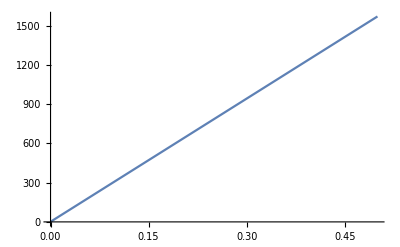

```mathematica
Plot[xmeanExpandedsteReduced/.ScalingSolnAsymptotic/.{ωx->500*2π,ωy->500*2π,λz->50*2π},{t,0,0.5}]
```

```mathematica
xmeanExpandedsteReducedSph=xmeanExpandedsteReduced/.{λx->λr,λy->λr,λz->λr}
```

Abs[λr]

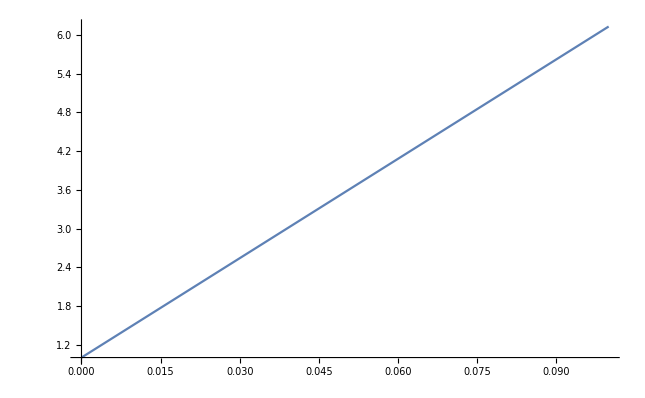

```mathematica
Plot[ xmeanExpandedsteReducedSph/.ScalingSolnAsymptoticSPH/.{ωr->10*2π},{t,0,0.10}]
```

```mathematica
Simplify[xmeanExpandedsteReduced/.ScalingSolnAsymptotic]
```

(√(-(1+(√2 t ωx^2)/(√(ωx (ωx+ωy))))^3 (1+(√2 t ωy^2)/(√(ωy (ωx+ωy)))) (1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2) (-7+3 (1+(√2 t ωx^2)/(√(ωx (ωx+ωy))))^2+(1+(√2 t ωy^2)/(√(ωy (ωx+ωy))))^2+(1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2)^2)))/(√2)

```mathematica
FullSimplify[xmeanExpandedsteReduced/.ScalingSolnAsymptotic]
```

(√(-(1+(√2 t ωx^2)/(√(ωx (ωx+ωy))))^3 (1+(√2 t ωy^2)/(√(ωy (ωx+ωy)))) (1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2) (-7+3 (1+(√2 t ωx^2)/(√(ωx (ωx+ωy))))^2+(1+(√2 t ωy^2)/(√(ωy (ωx+ωy))))^2+(1+(π t (ωx+ωy-ωz) ωz^2)/(ωx+ωy)^2)^2)))/(√2)

```mathematica
xmeanExpandedste=FullSimplify[(((((√xsqintExpanded)/(√(N QE))/.{chempot->chempotval})/.{abar->abarval})/.{omegabar->omegabarval})/.{U0->U0val}),Assumptions->assum]
```

(15^(1/5) √(-λx^3 λy λz (-7+3 λx^2+λy^2+λz^2)) ((a N ωy ωz ℏ^2)/(mass^2 ωx^4))^(1/5))/(√14 √(N QE))

```mathematica
FullSimplify[ExpandAll[xmeanste]]
```

(15^(1/5) ((a N ωy ωz ℏ^2)/(mass^2 ωx^4))^(1/5))/(√7 √(N QE))

# Messing with a gaussain

```mathematica
gauss=Exp[-(x-μ)^2/(2 σ^2)]
Integrate[gauss,{x,-∞,∞}]
```

ⅇ^(-(x-μ)^2/(2 σ^2))

$Aborted

# Old way (Cartesian)

gets very messy very quickly

```mathematica
harmPot[x_,y_,z_]=1/2 mass (ωx^2 x^2+ωy^2 y^2+ωz^2 z^2);

densityTF[x_,y_,z_]=( chempot-harmPot[x,y,z])/U0
```

(chempot-1/2 mass (x^2 ωx^2+y^2 ωy^2+z^2 ωz^2))/U0

```mathematica
omegabarval=(ωx ωy ωz )^(1/3);
chempotval:=15^(2/5)/2((N a)/abar)^(2/5)ℏ omegabar
abarval:=√(ℏ/(mass omegabar))
```

```mathematica
assum={mass∈Reals,mass>0,chempot∈Reals,chempot>0,ωx∈Reals,ωx>0,ωy∈Reals,ωy>0,ωz∈Reals,ωz>0};
```

Now we set up to do the integral to find the mean position 
we must first find an equation for the bounds of the chempot = harmPot[x,y,z] in each axis as a function of the other axes

```mathematica
RTFxyz={Solve[chempot==harmPot[xs,0,0],xs],Solve[chempot==harmPot[0,xs,0],xs],Solve[chempot==harmPot[0,0,xs],xs]}
```

{{{xs→-(√2 √chempot)/(√mass ωx)},{xs→(√2 √chempot)/(√mass ωx)}},{{xs→-(√2 √chempot)/(√mass ωy)},{xs→(√2 √chempot)/(√mass ωy)}},{{xs→-(√2 √chempot)/(√mass ωz)},{xs→(√2 √chempot)/(√mass ωz)}}}

check that the limits are the same value but ops. sign

```mathematica
RTFxyz[[;;,1,1,2]]===-RTFxyz[[;;,2,1,2]]
```

True

```mathematica
RTFxyz=RTFxyz[[;;,1,1,2]]
```

{-(√2 √chempot)/(√mass ωx),-(√2 √chempot)/(√mass ωy),-(√2 √chempot)/(√mass ωz)}

```mathematica
RTFfunxyz={Solve[chempot==harmPot[xs,y,z],xs],Solve[chempot==harmPot[x,ys,z],ys],Solve[chempot==harmPot[x,y,zs],zs]}
```

{{{xs→-(ⅈ √(-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2))/(√mass ωx)},{xs→(ⅈ √(-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2))/(√mass ωx)}},{{ys→-(ⅈ √(-2 chempot+mass x^2 ωx^2+mass z^2 ωz^2))/(√mass ωy)},{ys→(ⅈ √(-2 chempot+mass x^2 ωx^2+mass z^2 ωz^2))/(√mass ωy)}},{{zs→-(ⅈ √(-2 chempot+mass x^2 ωx^2+mass y^2 ωy^2))/(√mass ωz)},{zs→(ⅈ √(-2 chempot+mass x^2 ωx^2+mass y^2 ωy^2))/(√mass ωz)}}}

```mathematica
RTFfunxyz[[;;,1,1,2]]===-RTFfunxyz[[;;,2,1,2]]
```

True

```mathematica
RTFfunxyz=Simplify[RTFfunxyz[[;;,1,1,2]],Assumptions->assum]
```

{-(ⅈ √(-(2 chempot)/mass+y^2 ωy^2+z^2 ωz^2))/ωx,-(ⅈ √(-(2 chempot)/mass+x^2 ωx^2+z^2 ωz^2))/ωy,-(ⅈ √(-(2 chempot)/mass+x^2 ωx^2+y^2 ωy^2))/ωz}

```mathematica
RTFfunxyz[[1]]
```

-(ⅈ √(-(2 chempot)/mass+y^2 ωy^2+z^2 ωz^2))/ωx

```mathematica
Simplify[RTFfunxyz[[1]]/.{y->RTFxyz[[2]]*0.5,z->RTFxyz[[3]]*0.5},Assumptions->assum]
```

(1. √(chempot/mass))/ωx

```mathematica
norm=Integrate[
		densityTF[x,y,z],
		{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]},
		{y,-RTFfunxyz[[2]],RTFfunxyz[[2]]},
		{z,-RTFxyz[[3]],RTFxyz[[3]]},
		Assumptions->assum,
		GenerateConditions->False
		]
```

0

```mathematica
norm=Integrate[
				Integrate[
				densityTF[x,y,z],
				{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]},
				Assumptions->assum
			],
			{y,-RTFfunxyz[[2]],RTFfunxyz[[2]]},
			Assumptions->assum
		]
```

$Aborted

```mathematica
xint=Simplify[Integrate[
				densityTF[x,y,z],
				{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]},
				Assumptions->assum
			],Assumptions->assum]
```

(2 ⅈ (-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2)^(3/2))/(3 √mass U0 ωx)

```mathematica
yintindef=Integrate[xint,
			y,
			Assumptions->assum
		]
```

(ⅈ √(-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2) (-√mass y ωy (10 chempot-2 mass y^2 ωy^2-5 mass z^2 ωz^2) √((-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2)/(-2 chempot+mass z^2 ωz^2))+3 (-2 chempot+mass z^2 ωz^2)^(3/2) ArcSinh[(√mass y ωy)/(√(-2 chempot+mass z^2 ωz^2))]))/(12 mass U0 ωx ωy √(1+(mass y^2 ωy^2)/(-2 chempot+mass z^2 ωz^2)))

```mathematica
yintdef=Simplify[yintindef/.y->-RTFfunxyz[[1]] - yintindef/.y->RTFfunxyz[[1]]  ,Assumptions->assum]
```

$Aborted

```mathematica
norm=Integrate[xint,
			{y,-RTFfunxyz[[2]],RTFfunxyz[[2]]},
			Assumptions->assum
		]
```

$Aborted

```mathematica
{z,-RTFxyz[[3]],RTFxyz[[3]]},
```

```mathematica
meanx=Integrate[
		x densityTF[x,y,0],
		{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]},
		{y,-RTFfunxyz[[2]],RTFfunxyz[[2]]},
		{z,-RTFxyz[[3]],RTFxyz[[3]]},
		Assumptions->assum
		]
```

```mathematica
var=Integrate[
		x densityTF[x,y,0],
		{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]},
		{y,-RTFfunxyz[[2]],RTFfunxyz[[2]]},
		{z,-RTFxyz[[3]],RTFxyz[[3]]},
		Assumptions->assum
		]
```

```mathematica
innterint=Integrate[densityTF[x,y,0],
						{x,-RTFfunxyz[[1]],RTFfunxyz[[1]]}
						]
```

-(4 ⅈ chempot √(-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2))/(3 √mass U0 ωx)+(2 ⅈ √mass y^2 ωy^2 √(-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2))/(3 U0 ωx)-(ⅈ √mass z^2 ωz^2 √(-2 chempot+mass y^2 ωy^2+mass z^2 ωz^2))/(3 U0 ωx)

```mathematica
Simplify[innterint,Assumptions->assum]
```

-(ⅈ √(-(2 chempot)/mass+y^2 ωy^2+z^2 ωz^2) (4 chempot-2 mass y^2 ωy^2+mass z^2 ωz^2))/(3 U0 ωx)

```mathematica
{1,2}∈
```

True